## Recap of important topics from week 3

### Functions

You can declare a function like this:

```mathematica
MySimpleFunction[(*Function inputs*)]:=(*simple function of the variables*)
```

Or a more complicated, multi-line function like this:

```mathematica
MyFunction[(*Function inputs*)]:=Module[{(*local variables used in the function/module*)},
(*Code of the fucntion here; *)
(*First line without a semicolon gets returned from function*)
]
```

You can call functions in three ways like this:

```mathematica
MyFunction[a]
MyFunction@a
a//MyFunction
```

MyFunction[a]

MyFunction[a]

MyFunction[a]

### Heads

Recall that everything in Mathematica is actually just some function called on some sequence of inputs no matter how complex. The interface then displays many of these functions in more readable ways. 

To see what Head a certain output has, you can call Head on it.

Some examples we say last week include:

```mathematica
Head[{a,b,c,d}]
Head[2]
Head[2.5]
Head[2+3ⅈ]
Head[-Graphics3D-]
Head[f[]]
```

List

Integer

Real

Complex

Graphics3D

f

Along with these examples from the wolfram documentation page: https://reference.wolfram.com/language/tutorial/Expressions.html#4715
-Graphics-

## Patterns

Recall this example from last week:

```mathematica
BetterRecursiveFibonacci[0]=0;
BetterRecursiveFibonacci[1]=1;
BetterRecursiveFibonacci[n_Integer]:=BetterRecursiveFibonacci[n-1]+BetterRecursiveFibonacci[n-2]
BetterRecursiveFibonacci[10]
BetterRecursiveFibonacci[10.5]
```

55

BetterRecursiveFibonacci[10.5]

Remember that it doesn’t simplify the BetterRecursiveFibonacci function unless it is called on an integer because we declared it with n_Integer instead of just n_. Here both n_ and n_Integer are patterns in Mathematica and they are extremely useful!  

And patterns can be used for much more than just function declarations as well see later in this notebook. 

In fact, the first example I’ll show is their use along with a built in function called Cases, which returns all the cases in a list that match a given pattern.

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ},a_Integer]
```

{1,3,4,5,10}

So in this above example, we return all the integers. It also works on lists of lists, but you need to tell it what level of the list to look through. However we’re more interested on patterns in general today, so if that’s something you’re interested in I recommend reading the documentation page for Cases: https://reference.wolfram.com/language/ref/Cases.html

We’ll in the next several sections, we’ll be using Cases[] to explore the different patterns in Mathematica

#### The general pattern (_)

The most general case in Mathematica is a case which matches anything and this is what we saw when we were declaring functions normally, this “anything-goes” or “wildcard” case is the simple underscore. When we use this pattern, it matches anything!

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ},_]
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ},a_]
```

{1,2.2,3.1,3,4,5,10,2 ⅈ}

{1,2.2,3.1,3,4,5,10,2 ⅈ}

You can see that it works with or without a letter in front. So why would we put a letter in front? Well the short answer is it lets us do stuff with the symbols that match our case, for instance if we wanted to square each element that matches our case we could do something like this:

```mathematica
Cases[Cases[{1,2.2,3.1,3,4,5,10,2ⅈ},a_:>a^2]]
```

Cases[{1,4.84,9.61,9,16,25,100,-4}]

But more on this latter. The important thing is that you could either have a symbol like “a” before your pattern or nothing and case will still match it. The pattern is everything that comes after the “_” and not before. Something before the “_” essentially just gives that specific pattern a name.

#### Or-ing patterns and even more general matching? (_|_) and (__)

We’ve seen that patterns are typed using an “_” but are there even more general patterns? Well yes, it turns out there are. When you have a single “_” it is looking for a pattern which matches a single element. However, we can actually define patterns which match an arbitrary number of elements. For instance lets look at this example:

```mathematica
Cases[{f[a],f[b],f[c],f[a,b,c],g[a],g[b],g[c],g[a,b,c]},f[_]]
```

{f[a],f[b],f[c]}

We can see the pattern is only matched on f[a], f[b], f[c] but not on f[a, b, c] because “_” on its own will match anything except a sequence of things. In this case we could get around this by matching more than one sequence as follows.

```mathematica
Cases[{f[a],f[b],f[c],f[a,b,c],g[a],g[b],g[c],g[a,b,c]},f[_]|f[_,_,_]]
```

{f[a],f[b],f[c],f[a,b,c]}

Here the “|” symbol means “or” (distinct from the logical or operator we saw previously ∨, ||) and will match f[_] or f[_,_,_]. 

But what if we have a case like this instead: 
{f[a], f[b], f[c], f[a,b],f[a, b, c], g[a], g[b], g[c],g[a,b], g[a, b, c]}

Sure, you could add another case as f[_] | f[_,_]| f[_, _, _]

But there is a pattern which is even more general than “_” and that is the “__” pattern which will match any symbol or any sequence of symbols:

```mathematica
Cases[{f[a],f[b],f[c],f[a,b],f[a,b,c],g[a],g[b],g[c],g[a,b],g[a,b,c]},f[__]]
```

{f[a],f[b],f[c],f[a,b],f[a,b,c]}

We can see that it doesn’t matter how many symbols are in the sequence, __ will match the sequence regardless.

#### Head matching (_Head)

Lets now take another look at that first example of Cases I showed a few minutes ago

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ},a_Integer]
```

{1,3,4,5,10}

This case only matches integers, by what is this? Well, any time you type something after the “_” in a pattern it means only match expressions with a specific head. In this case we only match symbols whose Head is integer. See for yourself:

```mathematica
list={1,2.2,3.1,3,4,5,10,2ⅈ};
caseList=Cases[list,a_Integer]
Head/@list
Head/@caseList
```

{1,3,4,5,10}

{Integer,Real,Real,Integer,Integer,Integer,Integer,Complex}

{Integer,Integer,Integer,Integer,Integer}

So, in the same way, if we only wanted the decimals then we could do this instead:

```mathematica
list={1,2.2,3.1,3,4,5,10,2ⅈ};
caseList=Cases[list,a_Real]
Head/@list
Head/@caseList
```

{2.2,3.1}

{Integer,Real,Real,Integer,Integer,Integer,Integer,Complex}

{Real,Real}

Remember I said Heads were useful? This is why! They’re very useful in pattern matching.

#### Patterns by Boolean functions (?)

This last example may bring up a question: What if I want to match all real numbers and not just integers and decimals? Well in that case sure you could do something like _Integer|_Real but then look at this next case:

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ,√2},_Integer|_Real]
```

{1,2.2,3.1,3,4,5,10}

It misses √2? But why? we clearly want to match all numbers? Well, we’re only matching based on heads and the head of √2is actually Power not Integer or Real

```mathematica
Head[√2]
```

Power

Ok, so then maybe we use _Integer | _Real|_Power ? But then we’ll still miss fractions! And the problem only gets worse due to the vast number of heads there are to represent numerical quantities.

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ,√2,1/2},_Integer|_Real]
```

{1,2.2,3.1,3,4,5,10}

So using heads isn’t actually what we want in this case. What we want is to match all values which have a numerical value and thankfully Mathematica has a built in function for this. It’s called NumericQ and it returns either True or False depending on whether you give it a number or not. It’s pretty simple:

```mathematica
NumericQ[1]
NumericQ[√2]
NumericQ[2ⅈ]

NumericQ[a]
NumericQ[-Graphics3D-]
NumericQ[({{1, 2}, {3, 4}})]
```

True

True

True

False

False

False

In fact any time you see a function that ends with a capital “Q” in the wolfram language it means it’s expected to only ever return True or False. Nothing enforces this rule or stops you from breaking it with your own functions, but it is true of all the built in functions

Anyway, how can we go ahead and use this in our pattern matching? Well, we can do it using the “?” symbol after the “_” as follows:

```mathematica
Cases[{1,2.2,3.1,3,4,5,10,2ⅈ,√2,1/2,a,b,c},_?NumericQ]
```

{1,2.2,3.1,3,4,5,10,2 ⅈ,√2,1/2}

Whenever you type a pattern of the form _?SomeFunction it applies SomeFunction to every element it’s testing and only matches the pattern if SomeFunction returns true for a given element. Mathematica has a lot of these built in Q functions and they are often very useful! For instance, here is ImageQ

```mathematica
Cases[{a,1,3,√2,-Graphics-,4,5,-Graphics-,1/2},_?ImageQ]
```

{-Graphics-,-Graphics-}

We can also make our own “question” functions that do more specific things if we want. For example:

```mathematica
FunnyNumberQ[x_]:=Piecewise[{{True, x==7}, {True, x==69}, {True, x==420}, {False, x!=7∧x!=69∧x!=420}}]
Cases[{a,v,b,1,2,3,7,4,3,69,420,69,√2},_?FunnyNumberQ]
```

{7,69,420,69}

#### Patterns with conditions (/;)

Ok, now what if we want to do something like only select positive numbers from a list containing positive and negative numbers? This is where conditions start to become really helpful.  They essentially do all the same things you could do with the Boolean functions, but they can be much more readable and easy to use for simple cases. 

For the “positives only” example:

```mathematica
Cases[{-4,3,-4,-8,2,-9,3,9,8,10},a_?NumericQ/;0<=a]
```

{3,2,3,9,8,10}

Here we can see that when we name a value matching a pattern, conditions can be written after the pattern following “/;”

Unlike the Boolean functions, however, we actually get much more freedom. For instance lets look at the following list of 5,000 points:

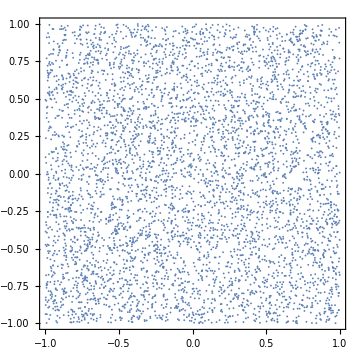

```mathematica
SeedRandom[1423];
pts=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{5000}];
ListPlot[pts,AspectRatio->1,ImageSize->Medium,Frame->True,PlotRange->{-1,1}]
```

Now lets say we only wanted to select all the points which lie in the unit circle. In other words points of the form {x,y} where √(x^2+y^2)<=1 Well then we can do the following

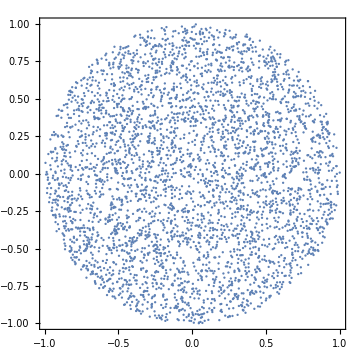

```mathematica
UnitCirclePts = Cases[pts,{x_,y_}/;√(x^2+y^2)<=1];
ListPlot[UnitCirclePts,AspectRatio->1,ImageSize->Medium,Frame->True,PlotRange->{-1,1}]
```

Pretty cool right? It’s extremely powerful, pretty intuitive, and very easy to read. And that’s exactly why we use Mathematica!

##### Cute little side note:

Also from these two lists we can actually approximate the value of π by taking the ratio of their sizes and multiplying by 4:

```mathematica
4(UnitCirclePts//Length)/(pts//Length)//N
```

3.1376

With more points you get closer and closer to the true value of π.

#### Conditions can be placed anywhere in the pattern

Also another really quick example. You don’t just have to place conditions at the end of a pattern. You can place them wherever you want as follows:

```mathematica
pts2={{-0.5032932785413267,0.6499802541062669},{-0.6391175287658508,-0.8068591352754955},{0.309489692740899,0.8500264615636492},{0.05299275198293474,-0.893873122696454},{0.7080796735699777,-0.603590571981266},{-0.35782158736317804,-0.4743965342593781},{-0.639553560313403,-0.864871432819617},{0.31382158916701863,0.2082262341086185},{0.28024647218030996,0.7487517561367554},{0.34160857709729964,-0.053395048800471745}};
Cases[pts2,{x_/;-0.5<=x<=0.5,y_}]
```

{{0.30949,0.850026},{0.0529928,-0.893873},{-0.357822,-0.474397},{0.313822,0.208226},{0.280246,0.748752},{0.341609,-0.053395}}

## Patterns Uses

#### Patterns in functions

Also remember, we can define functions suing patterns. And in fact we can use any patterns we want in their declaration no matter how complex. So if we wanted a function which only simplifies when you give it a number, we could do something like this:

```mathematica
ClearAll[NumericalFunction,NormalFunction,a]

NumericalFunction[a_?NumericQ]:=Cos[a]-1
NormalFunction[a_]:=Cos[a]-1

NumericalFunction[12]//N
NormalFunction[12]//N
NumericalFunction[a]//N
NormalFunction[a]//N
```

-0.156146

-0.156146

NumericalFunction[a]

-1.+Cos[a]

Or if we wanted something much more complicated, like a function that only simplified on a point containing a number between -1 and 1 and a picture then we could do something like this for-instance:

```mathematica
LightenImage[{Amount_?NumericQ/;-1<=Amount<=1,img_Image}]:=Piecewise[{{Lighter[img,Amount], Amount>=0}, {Darker[img,-Amount], Amount<0}}]
LightenImage[{0.5,-Graphics-}]
LightenImage[{-0.5,-Graphics-}]
LightenImage[{1.5,-Graphics-}]
LightenImage[{-0.5,0.5}]
```

-Graphics-

-Graphics-

LightenImage[{1.5,-Graphics-}]

LightenImage[{-0.5,0.5}]

#### Replacements (/.)

Another super useful application of functions is in replacement rules. These allow us to replace all instance in an expression which match a given pattern. 

A very simple case is using literal replacements as shown below:

```mathematica
D[Sin[x], x]/.{x->10}
```

Cos[10]

In this example we evaluate the derivative of Sin[x] at x=10 where /.{x->10} means replace the literal symbol x with 10. The important thing to note is that replacements are evaluated after the expression they’re to the right of. So first Mathematica computes the symbolic derivative of Sin[x] and then it plugs in 10

However, like I just said we can do much more than literal replacements, as we can also use patterns in the replacement rules for instance if we wanted to replace all integers with their reciprocal we could do the following:

```mathematica
ClearAll[f]
{a,b,2,3,4.5,f[4],f[3.3]}/.{a_Integer:>1/a}
```

{a,b,1/2,1/3,4.5,f[1/4],f[3.3]}

Or if we wanted to replace all numbers with 0

```mathematica
{a,b,2,3,4.5,f[4],f[3.3]}/.{a_?NumericQ:>0}
```

{a,b,0,0,0,f[0],f[0]}

Finally you can also apply multiple rules at once by placing them in a list as follows:

```mathematica
{a,b,2,3,4.5,f[4],f[3.3]}/.{a_?NumericQ:>0,f[x_]:>g[x]}
```

{a,b,0,0,0,g[4],g[3.3]}

I think you get the point. You can do replacements using any pattern your heart desires. 

However, note that when doing symbolic replacements you use “:>” and not “->”

The reason for this is explained at the end of this notebook

#### ReplaceRepeated (//.)

There is another version of replace which is even more aggressive. For instance consider the following case:

```mathematica
f[g[f[g[f[x]]]]]/.f[x_]:>h[x]
```

h[g[f[g[f[x]]]]]

This replacement rule only replaces the outer most occurrence of f[x] because at first the pattern matches f[g[f[g[f[x]]]]] with x = g[f[g[f[x]]]] and so it returns h[g[f[g[f[x]]]]] only. But what if we want to replace all instances of f with h? Well we could manually apply the rules three times like this:

```mathematica
f[g[f[g[f[x]]]]]/.f[x_]:>h[x]/.f[x_]:>h[x]/.f[x_]:>h[x]
```

h[g[h[g[h[x]]]]]

But this is a bad solution and it doesn’t scale well. So instead we could use //. which is the same as replace except it will keep replacing over and over until no more instances of the pattern are found

```mathematica
f[g[f[g[f[x]]]]]//.f[x_]:>h[x]
```

h[g[h[g[h[x]]]]]

Using these replacement rules you can do literally anything you want. In fact, this method of programing has its own name. It’s known as rule-based programing and like functional programing which we saw last week, it makes up its own coding paradigm. In fact, if you’re clever enough, you could simulate the behavior of any function using nothing but replacement rules. There are even some languages which work entirely based on rule definitions like Prolog. Because both functional and rule-based programing are possible in the wolfram language it is often referred to as a “multi-paradigm” language. 

Here is an example of us re-creating the Fibonacci function using nothing but replacement rules for instance:

```mathematica
ClearAll[f]
FibonacciRules = {f[0]->0,f[1]->1,f[n_Integer/;n>1]:>{n,0,1},{count_/;count>1,n1_,n2_}:>{count-1,n2,n1+n2},{1,n1_,n2_}:>n2};
f[10]//.FibonacciRules
```

55

Notice that calling f[10] does nothing because f is not a defined function. All of the logic is done using the replacement rules!

```mathematica
f[10]
```

f[10]

In this case, you’d probably never want to do this because it’s horribly unreadable, pretty complicated to figure out, and not that efficient. But in some cases there are problems which make much more sense to solve this way, and so being able to write rule based programs and function based ones in the same language is extremely powerful.

#### = vs := and -> vs :>

Finally the last thing I want to cover today is the difference between = and := along with the difference between -> and :> 

Personally I find it much easier to see what’s going on when comparing -> to :> by way of the following example:

```mathematica
{1,2.1,√2,a}/.{x_?NumericQ->Head[x]}
{1,2.1,√2,a}/.{x_?NumericQ:>Head[x]}
```

{Symbol,Symbol,Symbol,a}

{Integer,Real,Power,a}

We can see that when we use -> in the above example we get a list of symbols. This is because first Mathematica evaluates Head[x] which returns Symbol because x is a symbol and then it replaces every quantity which matches the pattern with “Symbol” In other words the expression first gets simplified to {1,2,3,a}/.{x_?NumericQ->Symbol} which then simplifies to {Symbol, Symbol, Symbol, a}

When we use :> (which means RuleDelayed) it waits until the rule values have been plugged in before it tries to do any simplification so it first gets simplified to  {Head[1],Head[2.1],Head[√2],a}  and then {Integer,Real,Power,a}   

The exact same thing is true with :=  (which means SetDelayed) except it happens when you’re declaring variables and functions. For instance:

```mathematica
ClearAll[f]
f[a_]=Head[a];
f[1]

ClearAll[f]
f[a_]:=Head[a]
f[1]
```

Symbol

Integer

So remember how I said you always want to use := for functions? Hopefully you can see why this is almost always the case. However, there are sometimes cases when you don’t want to do this. For-instance look at the following example (this is a PDE solution from one of my classes where I actually ran into this very issue):

```mathematica
Bi=0.9691814516034856;
λ=SolveValues[{λn BesselJ[1,λn]-BesselJ[0,λn]Bi==0,0<=λn<=10000},λn];
```

```mathematica
SlowSum[τ_]:=4Bi ∑_(n=1)^Length[λ] BesselJ[1,λ[[n]]]/(λ[[n]](λ[[n]]^2+Bi^2)BesselJ[0,λ[[n]]])ⅇ^(-λ[[n]]^2 τ);
FastSum[τ_]=4Bi ∑_(n=1)^Length[λ] BesselJ[1,λ[[n]]]/(λ[[n]](λ[[n]]^2+Bi^2)BesselJ[0,λ[[n]]])ⅇ^(-λ[[n]]^2 τ);
```

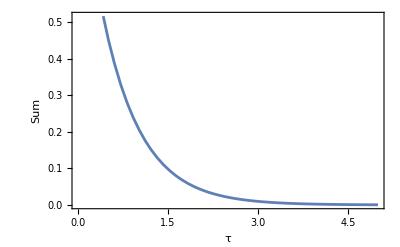
{2.77818,-Graphics-}

{0.232555,-Graphics-}

```mathematica
Quiet@AbsoluteTiming[Plot[SlowSum[τ],{τ,0,5},Frame->True,FrameLabel->{"τ","Sum"}]]
Quiet@AbsoluteTiming[Plot[FastSum[τ],{τ,0,5},Frame->True,FrameLabel->{"τ","Sum"}]]
```

Why is SlowSum almost an order of magnitude slower? It’s because for every point on the plot Mathematica has to symbolically expand the sum and then plug in the value of τ it’s trying to plot. However when we declare the function using = instead of := it symbolically evaluates the sum once in terms of the variable τ and then for each point Plot evaluate the function at, it only has to plug the τ value into the pre-expanded sum. This would be the same as declaring FastSum as follows:

```mathematica
FastSum[τ_]:=Evaluate[4Bi ∑_(n=1)^Length[λ] BesselJ[1,λ[[n]]]/(λ[[n]](λ[[n]]^2+Bi^2)BesselJ[0,λ[[n]]])ⅇ^(-λ[[n]]^2 τ)];
```

Also, I want to stress that this is not always the faster way to declare functions. 99% of the time you still want to use := when declaring functions. However in rare cases like this using = can be better.